# Homework 4: B-Spline Curves Due 4/29 by midnight

## Part 1. Implement the de Boor algorithm for a degree n B-Spline curve.

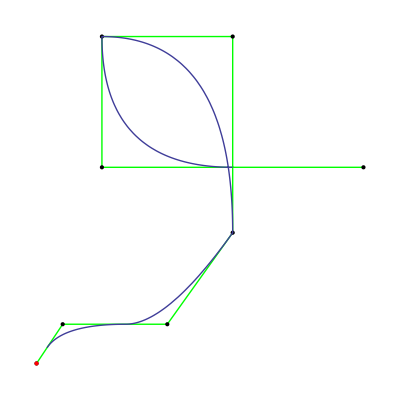

```mathematica
(* de Boor algorithm, setup from deBoor.nb *)
deBoor[k_,i_,u_]:=(
If [k==0,point = hwdata[[i]],point = ((knot[[i+n-k+1]]-u)*deBoor[k-1,i-1,u]+(u-knot[[i]])*deBoor[k-1,i,u])/(knot[[i+n-k+1]]-knot[[i]])];
t1 = (n+1) - (ii - i); (* interval points, I *)
t2 = k + 1; 
intermdeBoor[[t1,t2]] = point; (* save the interval points, I *)
Return[point];
);

evalutedeBoor[n_, u_]:= (
j = n+1;
While[(knot[[j]]≤    u ) && (j ≤ numknots-n - 1),j++];
ii = j-1; (* u's interval *)
point = deBoor[n,ii,u];
Return[point]
);
(* intermdeBoor holds all intermediate deboor points *)
intermdeBoor = Table[{0,0},{i,1,n+2},{j,1,n+2}];
(* deBoor points, curve degree, and knot sequence *)
n=2;
hwdata= {{0,0},{2,3},{10,3},{15,10},{15,25},{5,25},{5,15},{25,15}};
knot={0,0.3,0.5,0.8,1,1,2,2,3,4,4}; (* knot sequence *)
numknots = Length[knot];
(* setup the graphics variables *)
curve=ParametricPlot[evalutedeBoor[n,u],{u,knot[[n+1]],knot[[numknots-n]]}, PlotStyle->{Thick}]; 
poly=Graphics[{Thick,Green,Line[hwdata]}];
points=Graphics[{PointSize[Large],Point[hwdata]}];
begin= Graphics[{PointSize[Large],Red,Point[hwdata[[1]]]}];
Show[{poly,points, curve, begin}]
```

## Part 2. Apply deBoor algorithm to Manipulate u-domain.

```mathematica
(* createlevels function from deBoor.nb *)
levels = Table[{0},{i,1,n+1}];
createlevels[u_] := (
evalutedeBoor[n,u];
levels[[n+1]] = Graphics[{RGBColor[1.0, 0, 0],PointSize[Large],Point[intermdeBoor[[n+1,n+1]]]}];

Do[( 
myline = Table[{0,0},{j,1,n -l+2}];
Do[myline[[j]] = intermdeBoor[[l+j-1,l]],{j,1,n -l+2}];

levels[[l]] = Graphics[{RGBColor[0.3, 0.2, 0.7], Thick,  Line[{myline}], PointSize[Large],Point[{myline}]}]),
{l,n,2,-1}];

levels[[1]] = Graphics[{RGBColor[0.5, 0.3, 0.5],PointSize[Large],Point[intermdeBoor[[n+1,n+1]]]}];
);

domainu1 = knot[[n+1]];
domainu2 = knot[[numknots -n-1]];

(* the manipulate seems to get weird when u gets to the far right *)
Manipulate[
(createlevels[u];
Show[{ poly,points, curve, begin,levels}]),
{u,domainu1, domainu2}]
```

## Part 3. For degree 2, 3, and 4: plot all nth degree B-Splines for the knot sequence with full multiplicity at the ends and one simple knot in between.

```mathematica
knot1={0,0,0,1,1,1,2,3,4,4,4}; (* knot sequence for n = 2 *)
knot2={0,0,0,0,1,1,1,2,3,4,4,4}; (* knot sequence for n = 3 *)
knot3={0,0,0,0,0,1,1,2,3,4,4,4,5}; (* knot sequence for n = 4 *)
(* setup the graphics variables *)
curve1 = Graphics[{Thick,Red, BSplineCurve[hwdata, SplineDegree->2, SplineKnots->knot1, SplineWeights->Automatic]}]; (* degree 2 curve *)
curve2 = Graphics[{Thick,Magenta, BSplineCurve[hwdata, SplineDegree->3, SplineKnots->knot2, SplineWeights->Automatic]}];(* degree 3 curve *)
curve3 = Graphics[{Thick, Blue, BSplineCurve[hwdata, SplineDegree->4, SplineKnots->knot3, SplineWeights->Automatic]}];(* degree 4 curve *)
poly1=Graphics[{Thick,Green,Line[hwdata]}];
points1=Graphics[{PointSize[Large],Point[hwdata]}];
Show[{curve1,curve2, curve3,poly1, points1}, Axes->True, Ticks->Automatic]
```

-Graphics-

## Extra Credit 1: Implement the de Boor algorithm for knot sequences with any (valid) knot multiplicities ( demonstrate with 2 examples ).

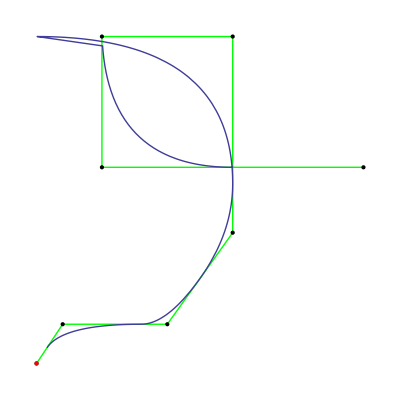

```mathematica
(* there seems to be an issue with these graphics using deBoor from Part 1 and the same knot sequence *)
(* using the same code from Part 1, and creating 2 different graphics with unique knot multiplicities , n = 2*)
n =2;
knot={0,0.3,0.5,0.8,0.9,1,1.3,1.2,2.6,4,4}; (* knot sequence *)
numknots= Length[knot];
(* setup the graphics variables for graphic 1 *)
curveEC1=ParametricPlot[evalutedeBoor[n,u],{u,knot[[n+1]],knot[[numknots-n]]}, PlotStyle->{Thick}]; 
polyEC1=Graphics[{Thick,Green,Line[hwdata]}];
pointsEC1=Graphics[{PointSize[Large],Point[hwdata]}];
beginEC1= Graphics[{PointSize[Large],Red,Point[hwdata[[1]]]}];
Show[{polyEC1,pointsEC1, curveEC1, beginEC1}]
```

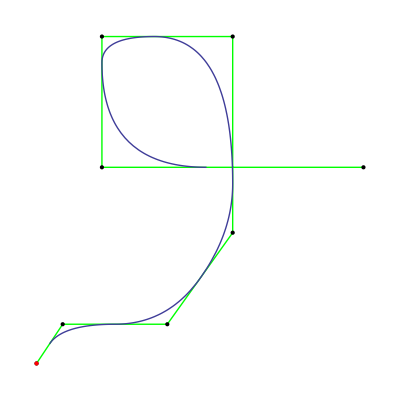

```mathematica
(* setup the graphics variables for graphic 2 *)
knot={0,0.6,0.7,0.8,0.9,1,1.3,1.5,2.3,3.5,3.8}; (* knot sequence *)
numknots= Length[knot];
curveEC2=ParametricPlot[evalutedeBoor[n,u],{u,knot[[n+1]],knot[[numknots-n]]}, PlotStyle->{Thick}]; 
polyEC2=Graphics[{Thick,Green,Line[hwdata]}];
pointsEC2=Graphics[{PointSize[Large],Point[hwdata]}];
beginEC2= Graphics[{PointSize[Large],Red,Point[hwdata[[1]]]}];
Show[{polyEC2,pointsEC2, curveEC2, beginEC2}]
```